```mathematica
Clear[x]
```

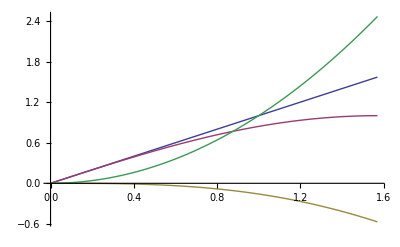

```mathematica
Plot[{x,Sin[x],Sin[x]-x,x^2},{x,0,Pi/2}]
```

```mathematica
Table[1/n,{n,1,20}]
L=Interpolation[Table[1/n^2,{n,1,20}],InterpolationOrder]
Plot[L[x],{x,1,20},PlotRange->{{0,20},{0,0.5}}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20}

Interpolation::inord: Value of option InterpolationOrder -> k should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

Interpolation[{1,1/4,1/9,1/16,1/25,1/36,1/49,1/64,1/81,1/100,1/121,1/144,1/169,1/196,1/225,1/256,1/289,1/324,1/361,1/400},InterpolationOrder→k]

Interpolation::inord: Value of option InterpolationOrder -> k should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

General::stop: Further output of Interpolation :: inord will be suppressed during this calculation.

-Graphics-

```mathematica
f=(1+#)&
```

1+#1&

```mathematica
f[2]
```

3

```mathematica
%
```

3

```mathematica
Function[1+#1 + #2][1,3]
```

5

```mathematica
(1+#1+#2)&[1,2]
```

4

```mathematica
g[1,2]
```

4

```mathematica
f[2]
```

1+x

```mathematica
D[{x,x^2,Sin[x],Cos[x],Tan[x]},x]
```

{1,2 x,Cos[x],-Sin[x],Sec[x]^2}